```mathematica
sim[dd_, scale_]:= Module[{d, sc},  d=dd; sc =scale; 
ϕ = d[[1]];
amplitude[t_]:=Module[{tt},  tt=t;
ret=0;
For[m=0, m≤ Length[d] - 2, m++, ret+=d[[m+2]]*Cos[m*ϕ + m*ω*tt]];
ret];
ω = 2*π*180;
U = 2π*1;
h=0;
a = .1;
end = (π/(a*2*U))*sc;
For[i=0, i≤12, i++, h += U*Cos[-i*ω*x - π/2 + a*amplitude[x]]];
s=NDSolve[{ⅈ*y'[x]==h*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
up = Evaluate[y[end]/.s][[1]];
s=NDSolve[{ⅈ*y'[x]==-h*y[x] ,y[0]==1/Sqrt[2]},y,{x,0,end}, MaxSteps->Infinity];
down = Evaluate[y[end]/.s][[1]];
Re[up*Conjugate[down] + down*Conjugate[up]];
{{Re[up], Im[up]}, {Re[down], Im[down]}}]
```

```mathematica
s=Import["~/repos/single_site_addressability/final_notebooks/elliptical2610.csv","String"];
data=ImportString[StringReplace[s," "->""],"Data"];
```

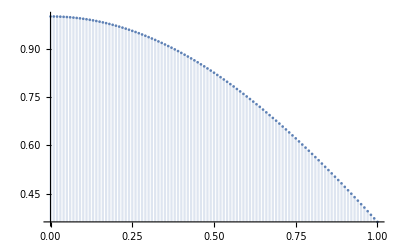

```mathematica
DiscretePlot[sim[data[[77]], k],{k, 0, 1, .01}]
```

```mathematica
data[[1]][[2]]
```

0.999884

```mathematica
simfull[dd_]:=sim[dd, 1]
Map[simfull, data]
```

{{{0.00197102,-0.707112},{0.00197102,0.707112}},{{0.321808,-0.629635},{0.321808,0.629635}},{{0.619808,-0.340352},{0.619808,0.340352}},{{0.692155,-0.144646},{0.692155,0.144646}},{{0.704353,-0.0623438},{0.704353,0.0623438}},{{0.706457,-0.0303166},{0.706457,0.0303166}},{{0.703412,-0.0721803},{0.703412,0.0721803}},{{0.701928,-0.0854269},{0.701928,0.0854269}},{{0.696258,-0.123391},{0.696258,0.123391}},{{0.661964,-0.248605},{0.661964,0.248605}},{{0.49682,-0.50316},{0.49682,0.50316}},{{0.300402,-0.640125},{0.300402,0.640125}},{{0.35184,-0.613358},{0.35184,0.613358}},{{0.321818,-0.62963},{0.321818,0.62963}},{{0.496826,-0.503155},{0.496826,0.503155}},{{0.300403,-0.640124},{0.300403,0.640124}},{{0.351842,-0.613357},{0.351842,0.613357}},{{0.529994,-0.468088},{0.529994,0.468088}},{{0.659488,-0.2551},{0.659488,0.2551}},{{0.699384,-0.104222},{0.699384,0.104222}},{{0.588546,-0.391936},{0.588546,0.391936}},{{0.491413,-0.508441},{0.491413,0.508441}},{{0.579526,-0.405154},{0.579526,0.405154}},{{0.650778,-0.276565},{0.650778,0.276565}},{{0.697314,-0.117269},{0.697314,0.117269}},{{0.703771,-0.0685928},{0.703771,0.0685928}},{{0.706298,-0.033806},{0.706298,0.033806}},{{0.702899,-0.0770346},{0.702899,0.0770346}},{{0.705107,-0.0530992},{0.705107,0.0530992}},{{0.704221,-0.0638313},{0.704221,0.0638313}},{{0.704311,-0.062827},{0.704311,0.062827}},{{0.706237,-0.0350696},{0.706237,0.0350696}},{{0.704322,-0.0626964},{0.704322,0.0626964}},{{0.704653,-0.0588683},{0.704653,0.0588683}},{{0.701963,-0.0851361},{0.701963,0.0851361}},{{0.702773,-0.0781713},{0.702773,0.0781713}},{{0.701176,-0.0913926},{0.701176,0.0913926}},{{0.694993,-0.13033},{0.694993,0.13033}},{{0.689551,-0.156589},{0.689551,0.156589}},{{0.608284,-0.360543},{0.608284,0.360543}},{{0.51181,-0.487904},{0.51181,0.487904}},{{0.65885,-0.256744},{0.65885,0.256744}},{{0.685464,-0.173607},{0.685464,0.173607}},{{0.696943,-0.119463},{0.696943,0.119463}},{{0.700608,-0.0956493},{0.700608,0.0956493}},{{0.702107,-0.0839462},{0.702107,0.0839462}},{{0.704414,-0.0616606},{0.704414,0.0616606}},{{0.705243,-0.0513128},{0.705243,0.0513128}},{{0.703055,-0.0755989},{0.703055,0.0755989}},{{0.697432,-0.116574},{0.697432,0.116574}},{{0.696262,-0.123371},{0.696262,0.123371}},{{0.661965,-0.248602},{0.661965,0.248602}},{{0.619811,-0.340347},{0.619811,0.340347}},{{0.692155,-0.144644},{0.692155,0.144644}},{{0.704354,-0.0623376},{0.704354,0.0623376}},{{0.70193,-0.0854141},{0.70193,0.0854141}},{{0.703415,-0.0721676},{0.703415,0.0721676}},{{0.706456,-0.0303268},{0.706456,0.0303268}},{{0.699386,-0.104208},{0.699386,0.104208}},{{0.659485,-0.255107},{0.659485,0.255107}},{{0.529987,-0.468097},{0.529987,0.468097}},{{0.491418,-0.508437},{0.491418,0.508437}},{{0.51179,-0.487926},{0.51179,0.487926}},{{0.608286,-0.360538},{0.608286,0.360538}},{{0.658851,-0.256741},{0.658851,0.256741}},{{0.685465,-0.173603},{0.685465,0.173603}},{{0.697433,-0.116568},{0.697433,0.116568}},{{0.703056,-0.0755843},{0.703056,0.0755843}},{{0.705243,-0.0513073},{0.705243,0.0513073}},{{0.704414,-0.0616716},{0.704414,0.0616716}},{{0.702107,-0.0839463},{0.702107,0.0839463}},{{0.700609,-0.0956458},{0.700609,0.0956458}},{{0.696943,-0.119466},{0.696943,0.119466}},{{0.694998,-0.130302},{0.694998,0.130302}},{{0.689553,-0.156581},{0.689553,0.156581}},{{0.650783,-0.276552},{0.650783,0.276552}},{{0.579523,-0.405157},{0.579523,0.405157}},{{0.697316,-0.117261},{0.697316,0.117261}},{{0.703772,-0.0685879},{0.703772,0.0685879}},{{0.701175,-0.0914011},{0.701175,0.0914011}},{{0.702773,-0.0781708},{0.702773,0.0781708}},{{0.701965,-0.085123},{0.701965,0.085123}},{{0.704654,-0.0588552},{0.704654,0.0588552}},{{0.704322,-0.0626933},{0.704322,0.0626933}},{{0.706237,-0.0350753},{0.706237,0.0350753}},{{0.704309,-0.0628429},{0.704309,0.0628429}},{{0.704219,-0.0638454},{0.704219,0.0638454}},{{0.705107,-0.0530992},{0.705107,0.0530992}},{{0.7029,-0.0770182},{0.7029,0.0770182}},{{0.706298,-0.0338293},{0.706298,0.0338293}},{{0.588546,-0.391936},{0.588546,0.391936}}}